{{0,0},{-(x^2 √(2+x^2))/(3 (1+x)^2)+(2 x √(2+x^2))/(3 (1+x))+(2 x (-√(1+x)+(2 √(2+x^2))/3))/(1+x)-(x^2 (-(√(1+x))/2+(2 √(2+x^2))/3))/(1+x)^2-(0.879646 Sin[x])/((2+x^2)^2),0.879646/(2+x^2)}}

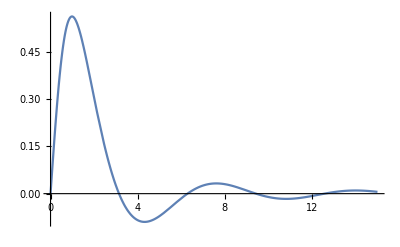

967.686

```mathematica
ClearAll["Global`*"];
ρ=1;
α=1;
ν = 0.035;
KR = 8*ν*Pi;
dt = 0.00025025025025025025;
A0 = x+1;
dA0 = D[A0,x];
β = x^2;
dβ = D[β,x];
B = { 0,  KR*Q/A + A/(A0*ρ)*dβ*(2/3*A^(1/2) - A0^(1/2)) - β/ρ*A/A0^2*dA0*( 2/3*A^(1/2) - 1/2*A0^(1/2) ) };
BU = { {D[B[[1]],A],D[B[[1]],Q]},{D[B[[2]],A],D[B[[2]],Q]} };
A = x^2+2;
Q = Sin[x];
BU/.A->x^2+2
F ={ Q , α*Q^2/A + β/(3*ρ*A0)*A^(3/2)};

H = {{0,1}, { -α*Q^2/A^2 + β/(2*ρ*A0)*A^(1/2), 2*α*Q/A }};

BU=Simplify[BU];
Plot[H[[2,2]],{x,0,15},PlotRange->All]
B[[2]]/.x->15
```